```mathematica
SetDirectory@NotebookDirectory[];
Import["QuESTlink.m"];
CreateLocalQuESTEnv["quest_link"];
```

## Parameters

```mathematica
model=5;(*4:S-Q error and hybrid sampling;*)
numQb=4;
numGt=numQb^2;
seed=-1;
ϵ=0.01;
SamSize=6;
SecSize=Ceiling[SamSize/2];
```

```mathematica
file=File["HS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
Data={};
AppendTo[Data,"model:"<>ToString[model]];
AppendTo[Data,"numQb:"<>ToString[numQb]];
AppendTo[Data,"numGt:"<>ToString[numGt]];
AppendTo[Data,"seed:"<>ToString[seed]];
AppendTo[Data,"eps:"<>ToString[ϵ]];
AppendTo[Data,"SamSize:"<>ToString[SamSize]];
AppendTo[Data,""];
Export[file,Data];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Gates

```mathematica
Clifford = Table[i*N[π,12]/2,{i,0,3,1}];
```

```mathematica
θ=RandomReal[{0,2*N[π,12]},3*numQb+6*numGt];
```

## Circuits

```mathematica
GateGraphGen[numQb_,numGt_,seed_]:=(
GateGraph={};
If[seed==-1,
depth=Ceiling[numGt/Floor[numQb/2]];
qINI=0;
Do[(
Do[(
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+1,numQb]];
),{q,qINI,numQb-1,2}];
qINI=1-qINI;
),{t,0,depth-1,1}];
AppendTo[GateGraph,Table[0,numQb-1]]
];
If[seed!=-1,
SeedRandom[seed];
Do[(
q=RandomInteger[{0,numQb-1}];
dis=RandomInteger[{1,numQb-1}];
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+dis,numQb]];
),{t,0,numGt-1,1}];
AppendTo[GateGraph,RandomInteger[{0,1},numQb-1]]
];
Return[GateGraph]
)
GateGraph=GateGraphGen[numQb,numGt,seed]
```

{0,1,2,3,1,2,3,0,0,1,2,3,1,2,3,0,0,1,2,3,1,2,3,0,0,1,2,3,1,2,3,0,{0,0,0}}

```mathematica
circuitIdeal[numQb_,numGt_,GateGraph_,θ_]:=(
circ={};
Do[(
AppendTo[circ,Subscript[Rz, q][θ[[3*q+1]]]];
AppendTo[circ,Subscript[Rx, q][θ[[3*q+2]]]];
AppendTo[circ,Subscript[Rz, q][θ[[3*q+3]]]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];
AppendTo[circ,Subscript[Rz, q1][θ[[3*numQb+6*t+1]]]];
AppendTo[circ,Subscript[Rx, q1][θ[[3*numQb+6*t+2]]]];
AppendTo[circ,Subscript[Rz, q1][θ[[3*numQb+6*t+3]]]];
AppendTo[circ,Subscript[Rz, q2][θ[[3*numQb+6*t+4]]]];
AppendTo[circ,Subscript[Rx, q2][θ[[3*numQb+6*t+5]]]];
AppendTo[circ,Subscript[Rz, q2][θ[[3*numQb+6*t+6]]]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

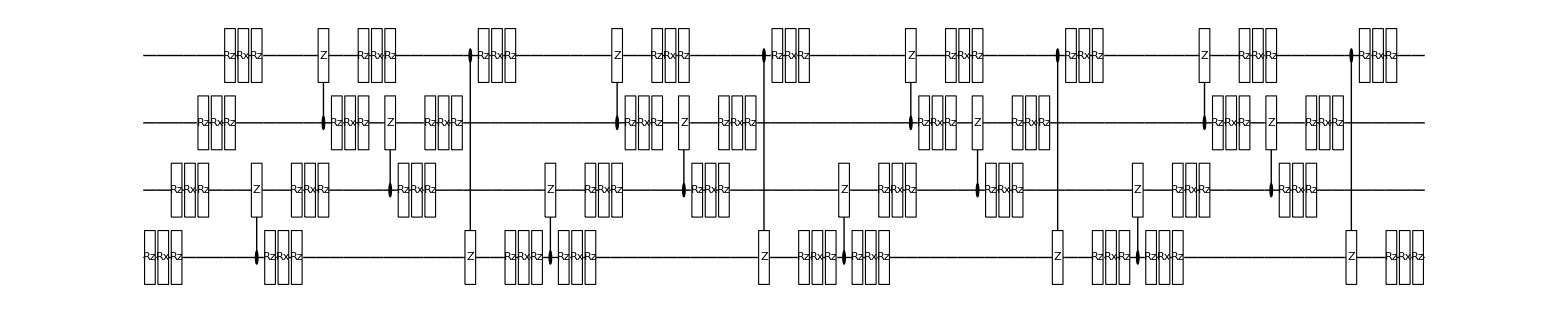

```mathematica
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
DrawCircuit@circI
```

```mathematica
circuitNoisy[numQb_,numGt_,GateGraph_,θ_,model_,ϵ_]:=(
circ={};
Do[(
the1=θ[[3*q+1]];
the2=θ[[3*q+2]];
the3=θ[[3*q+3]];
AppendTo[circ,Subscript[Rz, q][the1]];
AppendTo[circ,Subscript[Rx, q][the2]];
AppendTo[circ,Subscript[Rz, q][the3]];
AppendTo[circ,Subscript[Depol, q][ϵ/10*(the1+the2+the3)/(2*N[π,12])]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];AppendTo[circ,Subscript[Depol, q1,q2][ϵ]];
the1=θ[[3*numQb+6*t+1]];
the2=θ[[3*numQb+6*t+2]];
the3=θ[[3*numQb+6*t+3]];
AppendTo[circ,Subscript[Rz, q1][the1]];
AppendTo[circ,Subscript[Rx, q1][the2]];
AppendTo[circ,Subscript[Rz, q1][the3]];
AppendTo[circ,Subscript[Depol, q1][ϵ/10*(the1+the2+the3)/(2*N[π,12])]];
the1=θ[[3*numQb+6*t+4]];
the2=θ[[3*numQb+6*t+5]];
the3=θ[[3*numQb+6*t+6]];
AppendTo[circ,Subscript[Rz, q2][the1]];
AppendTo[circ,Subscript[Rx, q2][the2]];
AppendTo[circ,Subscript[Rz, q2][the3]];
AppendTo[circ,Subscript[Depol, q2][ϵ/10*(the1+the2+the3)/(2*N[π,12])]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

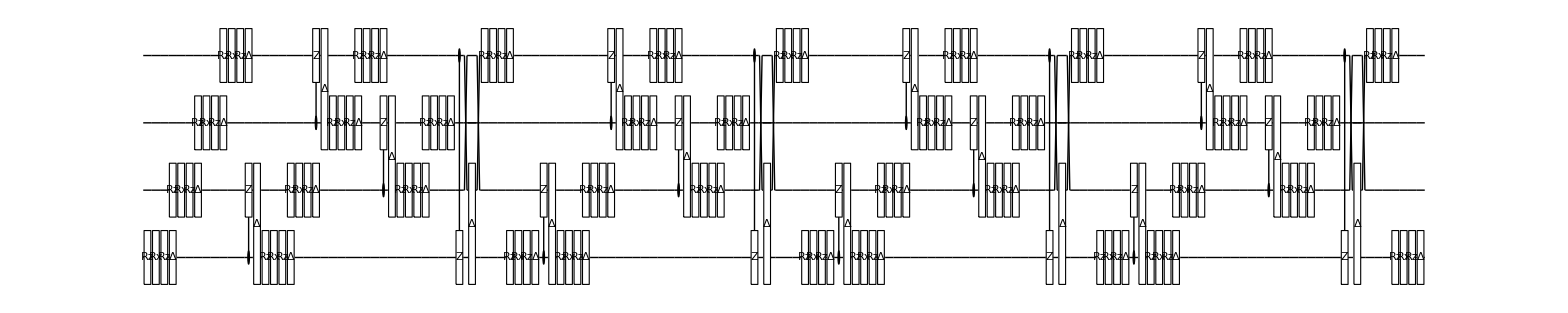

```mathematica
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
DrawCircuit@circN
```

## Sampling

```mathematica
SamplingU[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
θ=RandomReal[{0,2*N[π,12]},3*numQb+6*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,ZN-ZI];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SamplingC[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
numR=numQb+2*numGt;
Err1={};
Err2={};
Fid1={};
Fid2={};
Do[(
E1=0;E2=0;F1=0;F2=0;
Do[(
θ=RandomChoice[Clifford,3*numQb+6*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
E1=E1+(ZN-ZI);E2=E2+(ZN-ZI)^2;
F1=F1+(1-CalcFidelity[ρOUT,ψOUT]);
F2=F2+(1-CalcFidelity[ρOUT,ψOUT])^2;
),2(numR-1)^2];
E1=E1/(2(numR-1)^2);E2=E2/(2(numR-1)^2);
F1=F1/(2(numR-1)^2);F2=F2/(2(numR-1)^2);
AppendTo[Err1,E1];AppendTo[Err2,E2];
AppendTo[Fid1,F1];AppendTo[Fid2,F2];
),SamSize];
Return[{Err1,Fid1,Err2,Fid2}]
)
```

```mathematica
SamplingH[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
numR=numQb+2*numGt;
Err1={};
Err2={};
Fid1={};
Fid2={};
Do[(
E1=0;E2=0;F1=0;F2=0;
Do[(
Do[(
θ=RandomChoice[Clifford,3*numQb+6*numGt];
θ[[3i-2]]=RandomReal[{0,2*N[π,12]}];
θ[[3i-1]]=RandomReal[{0,2*N[π,12]}];
θ[[3i]]=RandomReal[{0,2*N[π,12]}];
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
E1=E1+(ZN-ZI);E2=E2+(ZN-ZI)^2;
F1=F1+(1-CalcFidelity[ρOUT,ψOUT]);
F2=F2+(1-CalcFidelity[ρOUT,ψOUT])^2;
),{i,1,numR}];
),2numR];
E1=E1/(2 numR^2);E2=E2/(2 numR^2);
F1=F1/(2 numR^2);F2=F2/(2 numR^2);
AppendTo[Err1,E1];AppendTo[Err2,E2];
AppendTo[Fid1,F1];AppendTo[Fid2,F2];
),SamSize];
Return[{Err1,Fid1,Err2,Fid2}]
)
```

## Simulation

Mon 9 Mar 2020 12:32:32GMT+8.

{0,1,2,3,1,2,3,0,0,1,2,3,1,2,3,0,0,1,2,3,1,2,3,0,0,1,2,3,1,2,3,0,{0,0,0}}

Mon 9 Mar 2020 12:38:37GMT+8.

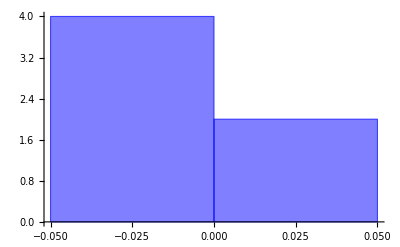

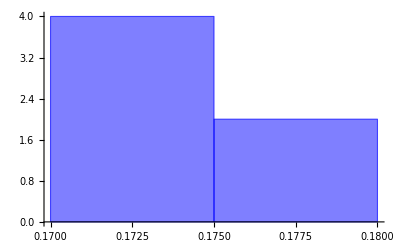

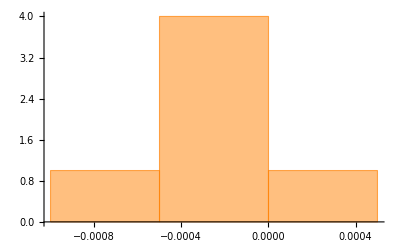

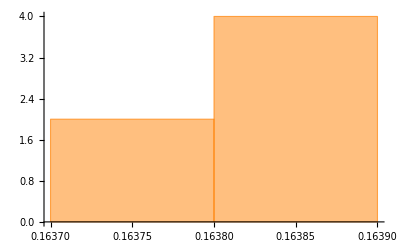

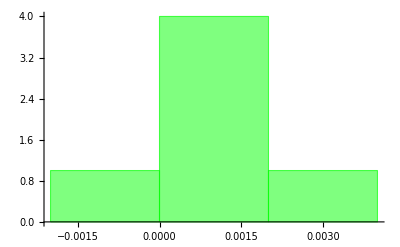

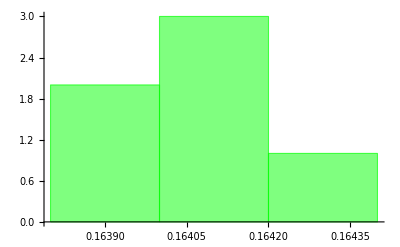

```mathematica
StartTime = Now
GateGraph=GateGraphGen[numQb,numGt,seed]
US=SamplingU[numQb,numGt,GateGraph,model,ϵ,SamSize];
fileT=File["HS-U.dat"];Export[fileT,US];
CS={};HS={};
Do[(
CST=SamplingC[numQb,numGt,GateGraph,model,ϵ,SecSize];
fileT=File["HS-C-"<>ToString[i]<>".dat"];Export[fileT,CST];
CS=Join[CS,Transpose[CST]];
HST=SamplingH[numQb,numGt,GateGraph,model,ϵ,SecSize];
fileT=File["HS-H-"<>ToString[i]<>".dat"];Export[fileT,HST];
HS=Join[HS,Transpose[HST]];
),{i,1,Ceiling[SamSize/SecSize]}];
CS=Transpose[CS];HS=Transpose[HS];
EndTime = Now

Histogram[US[[1]],ChartStyle->Opacity[.5,Blue]]
Histogram[US[[2]],ChartStyle->Opacity[.5,Blue]]
Histogram[CS[[1]],ChartStyle->Opacity[.5,Orange]]
Histogram[CS[[2]],ChartStyle->Opacity[.5,Orange]]
Histogram[HS[[1]],ChartStyle->Opacity[.5,Green]]
Histogram[HS[[2]],ChartStyle->Opacity[.5,Green]]

AppendTo[Data,"US-Err:"];AppendTo[Data,US[[1]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,US[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err1:"];AppendTo[Data,CS[[1]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid1:"];AppendTo[Data,CS[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err2:"];AppendTo[Data,CS[[3]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid2:"];AppendTo[Data,CS[[4]]];AppendTo[Data,""];
AppendTo[Data,"HS-Err1:"];AppendTo[Data,HS[[1]]];AppendTo[Data,""];
AppendTo[Data,"HS-Fid1:"];AppendTo[Data,HS[[2]]];AppendTo[Data,""];
AppendTo[Data,"HS-Err2:"];AppendTo[Data,HS[[3]]];AppendTo[Data,""];
AppendTo[Data,"HS-Fid2:"];AppendTo[Data,HS[[4]]];AppendTo[Data,""];
AppendTo[Data,"Start Time: "<>ToString[StartTime]];
AppendTo[Data,"End Time: "<>ToString[EndTime]];
Export[file,Data];
```

```mathematica
MUS=Table[Moment[US[[1]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[1]],m],{m,1,10,1}]
MHS=Table[Moment[HS[[1]],m],{m,1,10,1}]
MUS=Table[Moment[US[[2]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[2]],m],{m,1,10,1}]
MHS=Table[Moment[HS[[2]],m],{m,1,10,1}]
```

{-0.018901,0.000673561,-0.0000245566,9.46815×10^-7,-3.74585×10^-8,1.50186×10^-9,-6.06086×10^-11,2.45376×10^-12,-9.9501×10^-14,4.03822×10^-15}

{-0.000283347,1.57526×10^-7,-8.90096×10^-11,5.84434×10^-14,-4.00778×10^-17,2.84399×10^-20,-2.05121×10^-23,1.49385×10^-26,-1.09382×10^-29,8.03446×10^-33}

{0.000457015,9.17286×10^-7,1.42657×10^-9,2.90346×10^-12,5.6199×10^-15,1.13217×10^-17,2.26879×10^-20,4.57306×10^-23,9.21422×10^-26,1.85818×10^-28}

{0.173347,0.0300595,0.00521433,0.000904829,0.000157067,0.0000272746,4.73788×10^-6,8.23308×10^-7,1.43118×10^-7,2.48875×10^-8}

{0.163812,0.0268344,0.0043958,0.000720086,0.000117959,0.0000193231,3.16536×10^-6,5.18525×10^-7,8.49408×10^-8,1.39144×10^-8}

{0.16403,0.0269059,0.00441339,0.00072393,0.000118747,0.0000194781,3.19501×10^-6,5.2408×10^-7,8.59654×10^-8,1.4101×10^-8}